```mathematica
ClearAll


g1[n_]:=Sqrt[n];

g2[m_]:=Sqrt[m];
s=√10;
r=√10;

l=25;
```

ClearAll

```mathematica
Θ[τ_,p1_,p2_]:= τ/2 Cos[τ*(p1-p2)]-1/(4*p1)Sin[2*p1*τ];
q1[n_]:=Exp[-Abs[s]^2/2]*s^n/(√(n!));
q2[m_]:=Exp[-Abs[r]^2/2]*r^m/(√(m!));
```

```mathematica
f1[m_,n_]:=g1[n+1]*g2[m+1]*Sqrt[(n+1)*(m+1)];
f2[m_,n_]:=g1[n+2]*g2[m+2]*Sqrt[(n+2)*(m+2)];
f[m_,n_]:=Sqrt[f1[m,n]^2+f2[m,n]^2];
```

```mathematica
A[m_,n_,τ_,p1_,p2_]:=f1[m,n]^2/f[m,n]^2*Cos[2*Θ[τ,p1,p2]*f[m,n]]+f2[m,n]^2/f[m,n]^2;
```

```mathematica
B[m_,n_,τ_,p1_,p2_]:=-(I*f1[m,n])/(2*f[m,n])*Sin[2*Θ[τ,p1,p2]*f[m,n]];
```

```mathematica
Fm[m_,n_,τ_,p1_,p2_]:=(f1[m,n]*f2[m,n])/(2*f[m,n]^2)*(Cos[2*Θ[τ,p1,p2]*f[m,n]^2]-1);
```

```mathematica
R1[τ_,p1_,p2_]:=1/(4*π^2)*Abs[∑_(n=0)^l ∑_(m=0)^l q1[n]*q2[m]*A[m,n,τ,p1,p2]*Exp[-I*n*ϕ1]*Exp[-I*m*ϕ2]]^2;
```

```mathematica
R2[τ_,p1_,p2_]:=1/(4*π^2)*Abs[∑_(n=0)^l ∑_(m=0)^l q1[n]*q2[m]*B[m,n,τ,p1,p2]*Exp[-I*n*ϕ1]*Exp[-I*m*ϕ2]]^2;
```

```mathematica
R3[τ_,p1_,p2_]:=1/(4*π^2)*Abs[∑_(n=0)^l ∑_(m=0)^l q1[n]*q2[m]*Fm[m,n,τ,p1,p2]*Exp[-I*n*ϕ1]*Exp[-I*m*ϕ2]]^2;
```

```mathematica
R[τ_,p1_,p2_]:=R1[τ,p1,p2]+4*R2[τ,p1,p2]+4*R3[τ,p1,p2];
```

```mathematica
Ent[τ_,p1_,p2_] :=Module[{integral},integral=NIntegrate[R[τ,p1,p2]*Log[R[τ,p1,p2]],{ϕ1,0,2*π},
{ϕ2,0,2*π},Method->"LocalAdaptive",PrecisionGoal->6
];(1/Sqrt[2*Pi])*Exp[-integral]-1
];
```

```mathematica
uu1=Table[{τ,Re[Ent[τ,2,2]]},{τ,0.00001,5,0.01}];
uu2=Table[{τ,Re[Ent[τ,4,4]]},{τ,0.00001,5,0.01}];
uu3=Table[{τ,Re[Ent[τ,6,6]]},{τ,0.00001,5,0.01}];
```

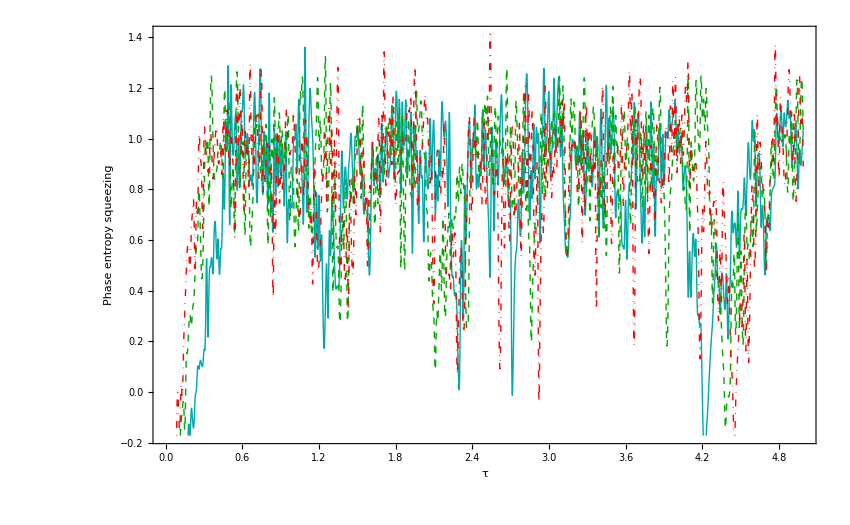

```mathematica
multient=ListPlot[{uu1,uu2,uu3},Joined->True,DataRange->{{0.00001,5},{-1,10}},Frame->True,FrameLabel->{τ,"Phase entropy squeezing  "},RotateLabel->True,PlotStyle->{{Darker[Cyan]},{Darker[Green],Dashed},{Red,DotDashed}},MaxPlotPoints->500,ImageSize->850,InterpolationOrder->2,LabelStyle->Directive[Green,35],FrameStyle->Directive[Blue,AbsoluteThickness[4]]]
```

```mathematica
Show[multient,PlotRange->{{0.00001,4},{-0.3,1.5}}]
```